```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bouyancy.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"visualizations.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"COM.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Stability.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"boats.m"}]]
```

```mathematica
avs[boat_,front_,guess_]:=Module[{},
FindRoot[rightingArm[boat,front,θ],{θ,guess},AccuracyGoal->3,PrecisionGoal->Infinity (*only accuracy used*)]
]
```

```mathematica
ClearAll[rightingArm]
```

```mathematica
rightingArm[boat,{0,1,0},θ]
```

rightingArm[<|name→A cube,massPts→{{0,0,0}},masses→{100},region→-Graphics3D-,graphics:>Show[-Graphics3D-,-Graphics3D-]|>,{0,1,0},θ]

```mathematica
nPoints=10000
```

10000

```mathematica
boatWaterline[boat,{0,0,1}]
```

111.769

1.04637

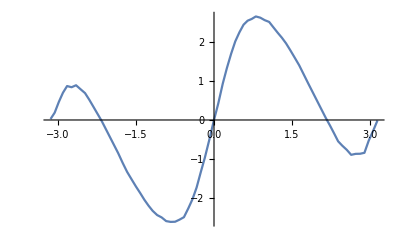

```mathematica
Plot[rightingArm[boat,{0,1,0},θ],{θ,-Pi,Pi},PlotPoints->20,MaxRecursion->2]
```

```mathematica
HoldForm@rightingArm[boat,{0,1,0},θ]
```

rightingArm[boat,{0,1,0},θ]

```mathematica
avs[boat,{0,1,0},-1.5]
rightingArm[boat,{0,1,0},θ]/.%
```

{θ→-2.18023}

-0.00480049